```mathematica
SetDirectory["C:\\Users\\Timothy\\Desktop"]
Directory[]
```

C:\Users\Timothy\Desktop

C:\Users\Timothy\Desktop

### Lattice with frames and simplices

#### now define vecδ, a set of slightly irregular triangle lattice coordinates

These were generated from starting with a regular triangular lattice and adding small displacements

```mathematica
Clear[vecδ];
vecδ=({{0.106317,0.129189},{1.1308,0.177425},{2.12509,0.153818},{3.15473,0.0850162},{0.564302,1.01804},{1.67532,1.00265},{2.65184,1.0378},{3.71669,1.06831},{1.06905,1.7747},{2.06606,1.81988},{3.19564,1.78468},{4.0628,1.74976},{1.5054,2.82035},{2.73961,2.6263},{3.64878,2.84453},{4.6619,2.84042}});
```

#### need to define ei (rotated frames) EACH TIME YOU RUN THIS THE FRAMES WILL ROTATE

Lattice basics

```mathematica
Clear[nv,ti]; 
(* Number of vertices *)
nv=16;
(* Canonical Frames *)
ti=Table[{{1,0},{0,1}},{i,1,nv}];
```

rotated frames

```mathematica
Clear[randangle,ei];
(* Random rotation angle for each vertex *)
randangle=Table[RandomReal[{0,π}],{i,1,nv}];
(* rotated frames *)
ei=Table[{{Cos[randangle[[i]]],Sin[randangle[[i]]]},{-Sin[randangle[[i]]],Cos[randangle[[i]]]}},{i,1,nv}];
```

frame graphics

```mathematica
Clear[frames1,frames2];
frames1=Table[Graphics[{Blue,Thickness[.0025],Arrowheads[.015],Arrow[{vecδ[[i]],1/3 ei[[i]][[1]]+vecδ[[i]]}]}],{i,1,nv}];
frames2=Table[Graphics[{Darker[Green,.4],Thickness[.0025],Arrowheads[.015],Arrow[{vecδ[[i]],1/3 ei[[i]][[2]]+vecδ[[i]]}]}],{i,1,nv}];
```

#### Circumcenter function

could be generalized to take an arbitrary set of vec locations

```mathematica
Clear[circumcenter];
circumcenter[i_,j_,k_]:={Solve[1/2(vecδ[[j]][[2]]+vecδ[[i]][[2]])-((vecδ[[j]][[1]]-vecδ[[i]][[1]])/(vecδ[[j]][[2]]-vecδ[[i]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[i]][[1]]))==1/2(vecδ[[j]][[2]]+vecδ[[k]][[2]])-((vecδ[[j]][[1]]-vecδ[[k]][[1]])/(vecδ[[j]][[2]]-vecδ[[k]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[k]][[1]])),x][[1]][[1]][[2]],1/2(vecδ[[j]][[2]]+vecδ[[k]][[2]])-((vecδ[[j]][[1]]-vecδ[[k]][[1]])/(vecδ[[j]][[2]]-vecδ[[k]][[2]]))(Solve[1/2(vecδ[[j]][[2]]+vecδ[[i]][[2]])-((vecδ[[j]][[1]]-vecδ[[i]][[1]])/(vecδ[[j]][[2]]-vecδ[[i]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[i]][[1]]))==1/2(vecδ[[j]][[2]]+vecδ[[k]][[2]])-((vecδ[[j]][[1]]-vecδ[[k]][[1]])/(vecδ[[j]][[2]]-vecδ[[k]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[k]][[1]])),x][[1]][[1]][[2]]-1/2(vecδ[[j]][[1]]+vecδ[[k]][[1]]))}
```

```mathematica
Clear[ccenter]; (* Alternate definition that takes an arbitrary list *)
ccenter[i_,j_,k_,list_]:={Solve[1/2(list[[j]][[2]]+list[[i]][[2]])-((list[[j]][[1]]-list[[i]][[1]])/(list[[j]][[2]]-list[[i]][[2]]))(x-1/2(list[[j]][[1]]+list[[i]][[1]]))==1/2(list[[j]][[2]]+list[[k]][[2]])-((list[[j]][[1]]-list[[k]][[1]])/(list[[j]][[2]]-list[[k]][[2]]))(x-1/2(list[[j]][[1]]+list[[k]][[1]])),x][[1]][[1]][[2]],1/2(list[[j]][[2]]+list[[k]][[2]])-((list[[j]][[1]]-list[[k]][[1]])/(list[[j]][[2]]-list[[k]][[2]]))(Solve[1/2(list[[j]][[2]]+list[[i]][[2]])-((list[[j]][[1]]-list[[i]][[1]])/(list[[j]][[2]]-list[[i]][[2]]))(x-1/2(list[[j]][[1]]+list[[i]][[1]]))==1/2(list[[j]][[2]]+list[[k]][[2]])-((list[[j]][[1]]-list[[k]][[1]])/(list[[j]][[2]]-list[[k]][[2]]))(x-1/2(list[[j]][[1]]+list[[k]][[1]])),x][[1]][[1]][[2]]-1/2(list[[j]][[1]]+list[[k]][[1]]))}
```

#### 4x4 irregular lattice with simplices

```mathematica
point=Graphics[Disk[{0,0},.002]];
```

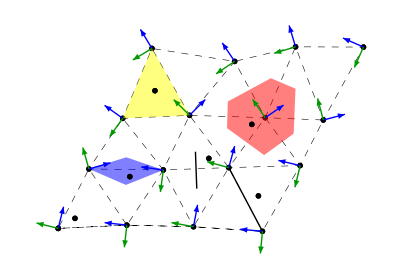

```mathematica
Show[

(* Dashed Lattice *)Graphics[{Dashed,Thickness[.001],Line[vecδ[[{1,2,5,1,2,3,6,2,3,4,7,3,4,8,7,6,5,9,6,10,7,11,8,12,11,10,9,13,10,14,11,15,12,16,15,14,13}]]]}],
(* Lattice Vertices *)
ListPlot[List/@(vecδ),PlotMarkers->{point, 0.015},PlotStyle->Black],
(* Subscript[σ, 0] *)
ListPlot[{vecδ[[1]]},PlotMarkers->{point,0.03},PlotStyle->Black],ListPlot[{vecδ[[1]]+{0.25,0.15}},PlotMarkers->{"σ_0",10},PlotStyle->Black],
(* Subscript[σ, 0]^* *)Graphics[{Opacity[.5,Red],Polygon[{circumcenter[14,10,11],circumcenter[11,14,15],circumcenter[11,15,12],circumcenter[11,12,8],circumcenter[11,8,7],circumcenter[11,7,10]}]}],ListPlot[{vecδ[[11]]-{.2,.1}},PlotMarkers->{"σ_0^*",10},PlotStyle->Black],
(* Subscript[σ, 2] *)Graphics[{Opacity[.5,Yellow],Polygon[{vecδ[[9]],vecδ[[10]],vecδ[[13]]}]}],ListPlot[{circumcenter[9,10,13]+{0,0}},PlotMarkers->{"σ_2",10},PlotStyle->Black],
(* Subscript[σ, 1]\[TensorWedge] Subscript[σ, 1]^* *)Graphics[{Opacity[.5,Blue],Polygon[{vecδ[[5]],circumcenter[5,6,2],vecδ[[6]],circumcenter[6,9,5]}]}],
ListPlot[{vecδ[[6]]-{.5,.1}},PlotMarkers->{"σ_1\[TensorWedge]σ_1^*",10},PlotStyle->Black],
(* Subscript[σ, 1]^* *)Graphics[{Thick,Line[{circumcenter[3,6,7],circumcenter[6,7,10]}]}],ListPlot[{circumcenter[6,7,10]+{.2,-0.1}},PlotMarkers->{"σ_1^*",10},PlotStyle->Black],
(* Subscript[σ, 1] *)
Graphics[{Thick,Line[{vecδ[[4]],vecδ[[7]]}]}],ListPlot[{circumcenter[4,7,8]+{-0.1,-0.1}},PlotMarkers->{"σ_1",10},PlotStyle->Black],
(* frames *)
frames1,frames2,Axes->False,AxesOrigin->{0,0}]
(*Export["latsimplexv1.pdf",%];*)
```

### Lattice vs dual lattice

Lets use similar coordinates as fig 2.1 for simplicity plus a couple extra vertices

#### define lattice points and vectors and frames

size of the lattaice

```mathematica
Clear[nv];
nv=16
```

16

Lattice site positions

```mathematica
Clear[vecδ];
vecδ=({{0.106317,0.129189},{1.1308,0.177425},{2.12509,0.153818},{3.15473,0.0850162},{0.564302,1.01804},{1.67532,1.00265},{2.65184,1.0378},{3.71669,1.06831},{1.06905,1.7747},{2.06606,1.81988},{3.19564,1.78468},{4.0628,1.74976},{1.5054,2.82035},{2.73961,2.6263},{3.64878,2.84453},{4.6619,2.84042},{4.12543,0.1350162},{2.52509,-0.653818}});
```

#### circumcenter function

```mathematica
Clear[circumcenter];
circumcenter[i_,j_,k_]:={Solve[1/2(vecδ[[j]][[2]]+vecδ[[i]][[2]])-((vecδ[[j]][[1]]-vecδ[[i]][[1]])/(vecδ[[j]][[2]]-vecδ[[i]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[i]][[1]]))==1/2(vecδ[[j]][[2]]+vecδ[[k]][[2]])-((vecδ[[j]][[1]]-vecδ[[k]][[1]])/(vecδ[[j]][[2]]-vecδ[[k]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[k]][[1]])),x][[1]][[1]][[2]],1/2(vecδ[[j]][[2]]+vecδ[[k]][[2]])-((vecδ[[j]][[1]]-vecδ[[k]][[1]])/(vecδ[[j]][[2]]-vecδ[[k]][[2]]))(Solve[1/2(vecδ[[j]][[2]]+vecδ[[i]][[2]])-((vecδ[[j]][[1]]-vecδ[[i]][[1]])/(vecδ[[j]][[2]]-vecδ[[i]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[i]][[1]]))==1/2(vecδ[[j]][[2]]+vecδ[[k]][[2]])-((vecδ[[j]][[1]]-vecδ[[k]][[1]])/(vecδ[[j]][[2]]-vecδ[[k]][[2]]))(x-1/2(vecδ[[j]][[1]]+vecδ[[k]][[1]])),x][[1]][[1]][[2]]-1/2(vecδ[[j]][[1]]+vecδ[[k]][[1]]))}
```

#### Fig 2.4

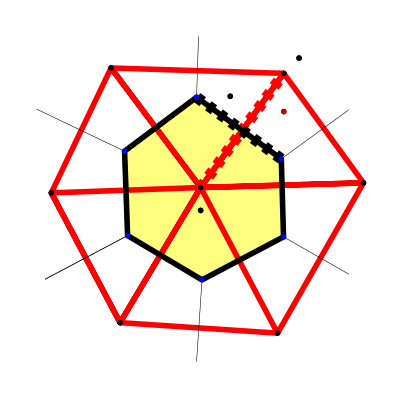

```mathematica
Show[
(*Shaded Subscript[σ, 1]^* *)
Graphics[{Opacity[.5,Yellow],Polygon[{circumcenter[3,4,7],circumcenter[4,8,7],circumcenter[8,11,7],circumcenter[10,11,7],circumcenter[6,10,7],circumcenter[3,6,7]}]}],

(*Lattice Links*)Graphics[{Red,Thickness[.01],Line[vecδ[[{3,4,7,3,6,7,3,6,10,7,10,11,7,11,8,7,8,4}]]]}],

(*Dual Latice Links*)
Graphics[{Black,Thickness[.001],Line[{circumcenter[3,4,7],circumcenter[3,6,7],circumcenter[6,10,7],circumcenter[10,11,7],circumcenter[11,8,7],circumcenter[8,4,7],circumcenter[3,4,7]}]}],
Graphics[{Black,Thickness[.001],Line[{circumcenter[3,6,7],circumcenter[2,3,6]}]}],Graphics[{Black,Thickness[.001],Line[{circumcenter[10,6,7],circumcenter[10,9,6]}]}],Graphics[{Black,Thickness[.001],Line[{circumcenter[11,10,7],circumcenter[10,11,14]}]}],Graphics[{Black,Thickness[.001],Line[{circumcenter[8,11,7],circumcenter[8,11,12]}]}],Graphics[{Black,Thickness[.001],Line[{circumcenter[3,6,7],circumcenter[2,3,6]}]}],Graphics[{Black,Thickness[.001],Line[{circumcenter[3,4,7],circumcenter[3,4,18]}]}],Graphics[{Black,Thickness[.001],Line[{circumcenter[4,8,7],circumcenter[4,8,17]}]}],

(* Subscript[ℓ, ij]*)
Graphics[{Red,Thickness[.02],Dashed,Line[vecδ[[{7,11}]]]}],

(* Subscript[S, ij]*)
Graphics[{Black,Thickness[.02],Dashed,Line[{circumcenter[7,8,11],circumcenter[7,11,10]}]}],

(*Lattice Vertices*)
ListPlot[vecδ[[{3,4,6,7,8,10,11}]],PlotStyle->Black,PlotMarkers->{Automatic,Medium}],

(* ∂Subscript[σ, 0]^* *)
Graphics[{Black,Thickness[.01],Line[{circumcenter[3,4,7],circumcenter[3,6,7],circumcenter[6,10,7],circumcenter[10,11,7],circumcenter[11,8,7],circumcenter[8,4,7],circumcenter[3,4,7]}]}],

(*Dual Lattice Vertices*)
ListPlot[{circumcenter[3,4,7],circumcenter[4,8,7],circumcenter[8,11,7],circumcenter[10,11,7],circumcenter[6,10,7],circumcenter[3,6,7]},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}],

(* Subscript[ℓ, ij]*)
ListPlot[{vecδ[[11]]+{0,-.25}},PlotMarkers->{"ℓ_ij",22},PlotStyle->Directive[Bold,Darker[Red,.25],FontFamily->"Comic Sans MS"]],

(* Subscript[S, ij]*)
ListPlot[{vecδ[[11]]+{-.35,-.15}},PlotMarkers->{"S_ij/2",18},PlotStyle->Directive[Bold,Black,FontFamily->"Comic Sans MS"]],

(* middle site i*)
ListPlot[{vecδ[[7]]+{0,-.15}},PlotMarkers->{"𝒾",18},PlotStyle->Directive[Black,FontFamily->"Comic Sans MS"]],

(* other site j*)
ListPlot[{vecδ[[11]]+{.1,.1}},PlotMarkers->{"𝒿",18},PlotStyle->Directive[Black,FontFamily->"Comic Sans MS"]]
]
(*Export["fig24V2.pdf",%];*)
```

### Curved Lattice elements

#### Simple triangles on curved lattice

```mathematica
Clear[y1s,y2s];
y1s={Graphics[{Blue,Arrowheads[.01],Arrow[{{5,2},{3,-.2}+{5,2}}]}],Graphics[{Blue,Arrowheads[.01],Arrow[{{10,7.5},{2.25,1.25}+{10,7.5}}]}],Graphics[{Blue,Arrowheads[.01],Arrow[{{15.5,8},{2.25,-1.25}+{15.5,8}}]}],Graphics[{Blue,Arrowheads[.01],Arrow[{{12,3},{-.2,-3}+{12,3}}]}]};
y2s={Graphics[{Green,Arrowheads[.01],Arrow[{{5,2},{.2,3}+{5,2}}]}],Graphics[{Green,Arrowheads[.01],Arrow[{{10,7.5},{-1.25,2.25}+{10,7.5}}]}],Graphics[{Green,Arrowheads[.01],Arrow[{{15.5,8},{1.25,2.25}+{15.5,8}}]}],Graphics[{Green,Arrowheads[.01],Arrow[{{12,3},{3,-.2}+{12,3}}]}]};
```

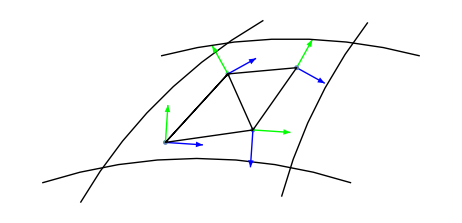

```mathematica
Show[(*ListPlot[{{0,0},{10,10},{15,0},{20,10}}],*)ListPlot[{{5,2},{10,7.5},{12,3},{15.5,8}},PlotMarkers->{Automatic,5}],y1s,y2s,Graphics[Line[{{5,2},{10,7.5},{12,3},{15.5,8},{10,7.5},{5,2},{12,3}}]],Graphics[Circle[{5 (1+Sqrt[31]),5 (1-Sqrt[31])},40,{π/2+π/6,π-π/6}]],Graphics[Circle[{15/2,-(5 √247)/2},40,{π/2-π/10,π/2+π/10}]],Graphics[Circle[{1/2 (35+2 Sqrt[1255]),1/2 (10-Sqrt[1255])},40,{π/2+π/4+π/24,π-π/12}]],Graphics[Circle[{15,10-15 Sqrt[7]},40,{π/2-π/12,π/2+π/12}]],Axes->False,AxesOrigin->{0,0},PlotRange->All,AspectRatio->Automatic]
(*Export["flattrioncurvedlattice.pdf",%]*)
```

#### curved lattice showing flat vs curved frames

```mathematica
Clear[Y1s,Y2s,X1s,X2s];
Y1s={Graphics[{Blue,Arrowheads[.02],Thickness[0.003],Arrow[{{0,0},3/2{3,-.2}+{0,0}}]}],Graphics[{Blue,Arrowheads[.02],Thickness[0.003],Arrow[{{10,10},3/2{2.25,.75}+{10,10}}]}],Graphics[{Blue,Arrowheads[.02],Thickness[0.003],Arrow[{{20,10},3/2{2.25,-1.25}+{20,10}}]}],Graphics[{Blue,Arrowheads[.02],Thickness[0.003],Arrow[{{15,0},3/2{-.2,-3}+{15,0}}]}]};
Y2s={Graphics[{Darker[Green,.4],Arrowheads[.02],Thickness[0.003],Arrow[{{0,0},3/2{.2,3}+{0,0}}]}],Graphics[{Darker[Green,.4],Arrowheads[.02],Thickness[0.003],Arrow[{{10,10},3/2{-.75,2.25}+{10,10}}]}],Graphics[{Darker[Green,.4],Arrowheads[.02],Thickness[0.003],Arrow[{{20,10},3/2{1.25,2.25}+{20,10}}]}],Graphics[{Darker[Green,.4],Arrowheads[.02],Thickness[0.003],Arrow[{{15,0},3/2{3,-.2}+{15,0}}]}]};
X1s={Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{0,0},3/2{3,.5}+{0,0}}]}],Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{10,10},3/2{2.25,.2}+{10,10}}]}],Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{20,10},3/2{2.25,-.25}+{20,10}}]}],Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{15,0},3/2{2.5,-.5}+{15,0}}]}]};
X2s={Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{0,0},1.25{2,3}+{0,0}}]}],Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{10,10},1.4{2,1.45}+{10,10}}]}],Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{20,10},2{.8,1.25}+{20,10}}]}],Graphics[{Black,Arrowheads[.02],Thickness[0.0025],Arrow[{{15,0},1.35{.8,2.5}+{15,0}}]}]};
```

```mathematica
Clear[vertexlabels,framelabels1,framelabels2,coordlabels1,coordlabels2];
vertexlabels=ListPlot[List/@{{0,0}-{1,.5},{10,10}-{0,.75},{15,0}-{.7,-.7},{20,10}-{1,.5}},PlotMarkers->{{"ψ_1",11.5},{"ψ_3",11.5},{"ψ_2",11.5},{"ψ_4",11.5}},PlotStyle->Black];
framelabels1=ListPlot[List/@{3/2{3,-.2}+{0,0}-{.75,.5},3/2{2.25,.75}+{10,10}+{0,.5},3/2{-.2,-3}+{15,0}-{.7,-.7},3/2{2.25,-1.25}+{20,10}-{.75,.5}},PlotMarkers->{{"y_1^(1)",7.5},{"y_1^(3)",7.5},{"y_1^(2)",7.5},{"y_1^(4)",7.5}},PlotStyle->Blue];
framelabels2=ListPlot[List/@{3/2{.2,3}+{0,0}-{.75,.5},3/2{-.75,2.25}+{10,10}-{.6,.2},3/2{3,-.2}+{15,0}-{.7,-.7},3/2{1.25,2.25}+{20,10}-{1.25,.25}},PlotMarkers->{{"y_2^(1)",7.5},{"y_2^(3)",7.5},{"y_2^(2)",7.5},{"y_2^(4)",7.5}},PlotStyle->Darker[Green,.4]];
coordlabels1=ListPlot[List/@{3/2{3,.5}+{0,0}+{0,.5},3/2{2.25,.2}+{10,10}-{0,.5},3/2{2.5,-.5}+{15,0}-{0,.7},3/2{2.25,-.25}+{20,10}+{.25,.5}},PlotMarkers->{{"x_1^(1)",7.5},{"x_1^(3)",7.5},{"x_1^(2)",7.5},{"x_1^(4)",7.5}},PlotStyle->Black];
coordlabels2=ListPlot[List/@{1.25{2,3}+{0,0}-{1,.25},1.4{2,1.45}+{10,10}-{1.5,.2},1.35{.8,2.5}+{15,0}-{1,.2},2{.8,1.25}+{20,10}+{.8,-.2}},PlotMarkers->{{"x_2^(1)",7.5},{"x_2^(3)",7.5},{"x_2^(2)",7.5},{"x_2^(4)",7.5}},PlotStyle->Black];
```

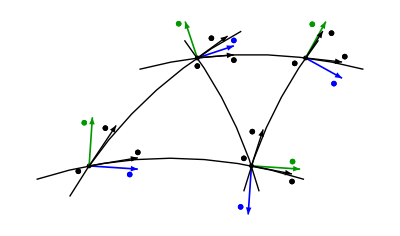

```mathematica
Show[ListPlot[{{0,0},{10,10},{15,0},{20,10}},PlotMarkers->Graphics[{Black, Disk[]},ImageSize->5]],vertexlabels,framelabels1,framelabels2,coordlabels1,coordlabels2,Y1s,Y2s,X1s,X2s,Graphics[Circle[{5 (1+Sqrt[31]),5 (1-Sqrt[31])},40,{π/2+π/6-π/90,π-π/6}]],Graphics[Circle[{15/2,-(5 √247)/2},40,{π/2-π/10,π/2+π/10}]],Graphics[Circle[{1/2 (35+2 Sqrt[1255]),1/2 (10-Sqrt[1255])},40,{π/2+π/4+π/24,π-π/12}]],Graphics[Circle[{15,10-15 Sqrt[7]},40,{π/2-π/12,π/2+π/12}]],Graphics[Circle[{1/2 (25-2 Sqrt[1255]),1/2 (10-Sqrt[1255])},40,{π/12,π/4-π/24}]],Axes->False,AxesOrigin->{0,0},PlotRange->All,AspectRatio->Automatic]
(*Export["curvedtrilattice.pdf",%]*)
```

### vierbein from one site to the next

#### points, lines, and arrows

```mathematica
pts={{0,0},{.25,0.273013},{.75,0.273013},{1,0}};
f=Graphics[{Blue,BezierCurve[pts]}];
g1=Graphics[{Red,Arrowheads[0.05],Thick,Arrow[{{0,0},{.22,.22}}]}];
g2=Graphics[{Red,Arrowheads[0.05],Thick,Arrow[{{1,0},{1-.22,.22}}]}];
p1=ListPlot[{{0,0}},PlotStyle->Black,PlotMarkers->{Automatic,Medium}];
p2=ListPlot[{{1,0}},PlotStyle->Black,PlotMarkers->{Automatic,Medium}];
```

#### plot

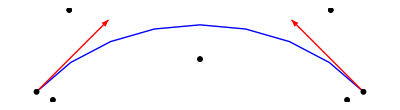

```mathematica
Show[
(*curve*)
f,
(*label*)
ListPlot[{{.5,.1}},PlotMarkers->{"Ω_𝒾𝒿",20},PlotStyle->Black],

(* vielbein 1 *)
g1,
(*label*)
ListPlot[{{.1,.25}},PlotMarkers->{"(e⃗)^((𝒾) 𝒿)",16},PlotStyle->Black],

(* vielbein 2 *)
g2,
(*label*)
ListPlot[{{.9,.25}},PlotMarkers->{"(e⃗)^((𝒿) 𝒾)",16},PlotStyle->Black],

(* point 1 *)
p1,
(* label *)
ListPlot[{{.05,-.025}},PlotMarkers->{"𝒾",14},PlotStyle->Black],

(* point 2 *)
p2,
(* label *)
ListPlot[{{.95,-.025}},PlotMarkers->{"𝒿",14},PlotStyle->Black]
]
(*Export["geoLink-3.pdf",%];*)
```